```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
<<MaTeX`
```

```mathematica
ℳ[μ_,ϵ_,α_]:=(1-ϵ)/(2 √(2 ⅇ^(-α^2)(Cosh[α^2]+(-1)^μ Cos[α^2])))+ϵ/(2 √(2 ⅇ^(-α^2)(Sinh[α^2]-(-1)^μ Sin[α^2])));

𝒩[μ_,α_]:=(1-μ)/(2 √(ⅇ^(-α^2)Cosh[α^2]))  + μ/(2 √(ⅇ^(-α^2)Sinh[α^2]));

p0[α_,γ_] :=  Cosh[γ  α^2]/(2 Cosh[α^2])(Cosh[(1-γ) α^2]+Cos[(1-γ) α^2]) ;
p1[α_,γ_] := Sinh[γ  α^2]/(2 Cosh[α^2])(Sinh[(1-γ) α^2]+Sin[(1-γ) α^2]) ;
p2[α_,γ_] :=  Cosh[γ  α^2]/(2 Cosh[α^2])(Cosh[(1-γ) α^2]-Cos[(1-γ) α^2]) ;
p3[α_,γ_] :=  Sinh[γ  α^2]/(2 Cosh[α^2])(Sinh[(1-γ)α^2]-Sin[(1-γ) α^2]) ;


𝒩0[α_]:=1/(√(1+2Re[a b*] Cos[ α^2]/Cosh[α^2]));
𝒩1[α_]:=1/(√(1-2Re[a b*] Sin[ α^2]/Sinh[α^2]));
𝒩2[α_]:=1/(√(1-2Re[a b*] Cos[ α^2]/Cosh[α^2]));
𝒩3[α_]:=1/(√(1+2Re[a b*] Sin[ α^2]/Sinh[α^2]));


p0Tilde[a_,b_,α_,γ_] =( (𝒩0 [α])/𝒩0[√γ α])^2  p0[α,γ];
p1Tilde[a_,b_,α_,γ_] = ((𝒩0 [α])/𝒩1[√γ α])^2 p1[α,γ] ;
p2Tilde[a_,b_,α_,γ_] = (𝒩0[α]/𝒩2[√γ α])^2 p2[α,γ] ;
p3Tilde[a_,b_,α_,γ_] =( 𝒩0[α]/𝒩3[√γ α])^2 p3[α,γ] ;

ClearAll[PC]
PC[a_,b_,α_,γ_]=p0Tilde[a,b,α,γ]+p1Tilde[a,b,α,γ];
```

## Success Probability

#### Ideal Tele-amp

```mathematica
FullSimplify[ComplexExpand[∑_(j=0)^3 ∑_(k=0)^3 (-1)^(1 Mod[j,2])(-1)^(1 Mod[k,2])ⅇ^(-(g1 α)^2(1-ⅈ^(-j+k)))]-1/ℳ[1,0,g1 α]^2]
```

0

```mathematica
ℳ[0,1,α]
```

1/(2 √2 √(ⅇ^(-α^2) (-Sin[α^2]+Sinh[α^2])))

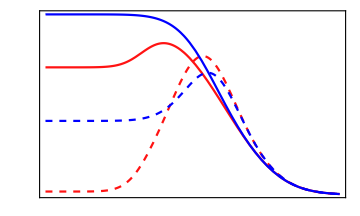

```mathematica
ClearAll[α,g];

PsTeleamp[pm_,α_,g_]:=N[(ℳ[0,1,α/(√(1/(1+g^2)))] ⅇ^(-α^2)α^3/2)^2(ℳ[pm,0,α]/1)^2 ∑_(j=0)^3 ∑_(k=0)^3 (-1)^(pm Mod[j,2])(-1)^(pm Mod[k,2])ⅇ^(-(g α)^2(1-ⅈ^(-j+k)))];

PsPlot[glist_]:=Module[{g,α,a,ℽ,b,T1, γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam, magni ,red , blue, green},
T1=1;(* no ZPS *)

fam = "CMU Serif";
axesLabelSize=20;
magni =axesLabelSize/12;

red   = RGBColor["#FF1313"];
blue = RGBColor["#0000FF"];
green =  RGBColor["#03C04A"];

txt[T2_,x_,y_] :=Graphics[ Text[Style[MaTeX["T ="<>ToString[T2],Magnification->magni]],{x,y},{0,0}]];

plt = Plot[{
PsTeleamp[0,α,glist[[1]]],
PsTeleamp[1,α,glist[[1]]],
PsTeleamp[0,α,glist[[2]]],
PsTeleamp[1,α,glist[[2]]]
},{α, 10^-3,2.5},PlotRange->Full,LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},Frame->True,FrameStyle->BlackFrame,ImageSize->Medium,PlotStyle->{{red,Dashed},{red},{blue, Dashed},{blue}},PlotRange->All,PlotRangeClipping->False,ImagePadding->{{65, 15}, {65, 35}},PlotRangePadding->None,
FrameLabel->{{MaTeX["P_{\\rm{s}}(\\times 10^{-3})",Magnification->magni],None},{MaTeX["\\alpha",Magnification->magni],None}},AspectRatio->0.6,
FrameTicks->{{Table[{x ,MaTeX[Round[x 10^3 ],"DisplayStyle"->False,Magnification->magni]},{x,N[{0,4 10^-3,8 10^-3,12 10^-3}]}],Automatic},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0,0.5,1,1.5,2,2.5,3}}],Automatic}}
];
g = Show[{plt  }]
]
plt = PsPlot[{2.5,1.25}]
(*Export["Ps-ideal-teleamp.pdf",plt]*)
```

#### Ideal ZPS

```mathematica
<<MaTeX`
```

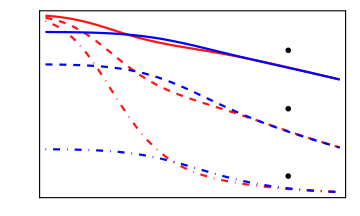

```mathematica
PsZPS[a_,b_,α_,T_]=(𝒩[0,α]/𝒩[0,√T α])^2(𝒩0[α]/𝒩0[√T α])^2 ⅇ^(-(1-T)α^2);
PsPlot[T2list_]:=Module[{a,ℽ,b,g,T1, γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam, magni ,red , blue, green},
T1=1;(* no ZPS *)

fam = "CMU Serif";
axesLabelSize=20;
magni =axesLabelSize/12;

red   = RGBColor["#FF1313"];
blue = RGBColor["#0000FF"];
green =  RGBColor["#03C04A"];

txt[T2_,x_,y_] :=Graphics[ Text[Style[MaTeX["T ="<>ToString[T2],Magnification->magni]],{x,y},{0,0}]];

plt = Plot[{
PsZPS[√0.5,√0.5,α,T2list[[1]]],
PsZPS[√0.5,-√0.5,α,T2list[[1]]],
PsZPS[√0.5,√0.5,α,T2list[[2]]],
PsZPS[√0.5,-√0.5,α,T2list[[2]]],
PsZPS[√0.5,√0.5,α,T2list[[3]]],
PsZPS[√0.5,-√0.5,α,T2list[[3]]]
},{α,1,3},PlotRange->{0,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},Frame->True,FrameStyle->BlackFrame,ImageSize->Medium,PlotStyle->{{red,DotDashed},{blue,DotDashed},{red,Dashed},{blue,Dashed},{red},{blue}},PlotRange->All,PlotRangeClipping->False,ImagePadding->{{65, 15}, {65, 35}},PlotRangePadding->None,
FrameLabel->{{MaTeX["P_{\\rm{s}}",Magnification->magni],None},{MaTeX["\\alpha",Magnification->magni],None}},AspectRatio->0.6,
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0,0.2,0.4,0.6,0.8,1}}],Automatic},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0,0.5,1,1.5,2,2.5,3}}],Automatic}}
];
g = Show[{plt,txt[T2list[[1]],2.65,0.10] ,txt[T2list[[2]],2.65,0.475] ,txt[T2list[[3]],2.65,0.8]  }]
];
plt= PsPlot[{0.50,0.85,.95}]
(*Export["Ps-ideal-zps.pdf",plt]*)
```

## Realistic Setup

```mathematica
ClearAll[ηp,R1,RB,TB,R2,gp,gpp,R1p];
ηp[T_,η_] := T/(1-η (1-T));

R1[γ_,ηp_] := 1-ηp γ;

RB[g_]:= 1/(1+g^2);
TB[g_] :=g^2/(1+g^2);

R2[g_,RE_,η_] :=((RE(1+g^2))/(1-RE)+2(1-η))/(g^2+(RE(1+g^2))/(1-RE)+2(1-η));

gp[g_,R2_] :=g/(√(1-R2));
gpp [gp_,R1_]:=√(gp^2 (1-R1)+R1);
R1p[g_,R1_] := R1/(g^2+R1-g^2 R1);
```

```mathematica
FullSimplify[T/ηp gpp^2(1-R1p)(1-R2),{0<T<=1,0<η<=1,0<=RE<1,g>0}]
```

(gpp^2 (-1+R1p) (-1+R2) T)/ηp

```mathematica
FullSimplify[T/ηp[T,η] gpp[gp[g,R2[g,RE,η]],R1[γ,ηp[T,η]]]^2(1-R1p[g,R1[γ,ηp[T,η]]])(1-R2[g,RE,η]),{0<T<=1,0<η<=1,0<=RE<1,g>0}]
```

(g^4 T γ (1-RE+T γ+g^2 T γ+(-1+RE) (1+T (-1+2 γ)) η))/((2+g^2-RE+2 (-1+RE) η) (1-η+T ((-1+g^2) γ+η)))

```mathematica
coeflist = Simplify[CoefficientList[FullSimplify[(g^4 T γ (1-RE+T γ+g^2 T γ+(-1+RE) (1+T (-1+2 γ)) η)-(2+g^2-RE+2 (-1+RE) η) (1-η+T ((-1+g^2) γ+η)))/.{g->√G}],G]];
FullSimplify[∑_(k=1)^4 coeflist[[k]] g^(2(k-1))-(g^4 T γ (1-RE+T γ+g^2 T γ+(-1+RE) (1+T (-1+2 γ)) η)-(2+g^2-RE+2 (-1+RE) η) (1-η+T ((-1+g^2) γ+η)))]
```

0

```mathematica
coeflist//MatrixForm
```

((-1+T (γ-η)+η) (2-2 η+RE (-1+2 η))
-1+η-T (η+(-1+RE) γ (-1+2 η))
T γ (-RE+T γ+(-1+RE) (1+T (-1+2 γ)) η)
T^2 γ^2)

```mathematica
Manipulate[Quiet[Solve[((T/ηp gpp^2(1-R1p)(1-R2))/.{T->Tc,γ->γc,RE->REc,η->ηc})==1,{g}]//MatrixForm],{Tc,0.5,1},{γc,0.5,1},{REc,0,0.99},{ηc,0.5,1}]
```

```mathematica
soln=Solve[((T/ηp[T,η] gpp[gp[g,R2[g,RE,η]],R1[γ,ηp[T,η]]]^2(1-R1p[g,R1[γ,ηp[T,η]]])(1-R2[g,RE,η])))==1,{g^2}];
```

```mathematica
Simplify[soln/.{T->0.5,γ->0.95,RE->0.01,η->0.95}]
```

{{g→-1.45298+2.38782×10^-18 ⅈ},{g→1.45298-2.38782×10^-18 ⅈ},{g→-2.65429×10^-16+0.364917 ⅈ},{g→2.65429×10^-16-0.364917 ⅈ},{g→-4.08469×10^-16-0.293124 ⅈ},{g→4.08469×10^-16+0.293124 ⅈ}}

Second entry gives real solution g >= 1

```mathematica
ClearAll[g];
g[γ_,T_,η_,RE_]=g/.soln[[2]];
```

```mathematica
ClearAll[g];
g[γ_,T_,η_,RE_]:=(1/(√6))(√(-(1/(T γ))2 (-η+T (γ+η-2 γ η)+RE (-1+η+T (-1+2 γ) η))+(2 2^(1/3) (3-3 η+η^2+T^2 (γ+η-2 γ η)^2+RE^2 (-1+η+T (-1+2 γ) η)^2+T (-3+2 η) (-η+γ (-1+2 η))-RE (2 (-1+η) η+2 T^2 (-1+2 γ) η (-η+γ (-1+2 η))+T (2 (1-2 η) η+γ (5-12 η+8 η^2)))))/((9 RE T^3 γ^3+2 RE^3 T^3 γ^3+45 T^4 γ^4-18 RE T^4 γ^4-15 RE^2 T^4 γ^4-63 T^5 γ^5+42 RE T^5 γ^5-2 T^6 γ^6+9 T^3 γ^3 η-18 RE T^3 γ^3 η+6 RE^2 T^3 γ^3 η-6 RE^3 T^3 γ^3 η-9 T^4 γ^3 η+18 RE T^4 γ^3 η-6 RE^2 T^4 γ^3 η+6 RE^3 T^4 γ^3 η-72 T^4 γ^4 η+15 RE T^4 γ^4 η+51 RE^2 T^4 γ^4 η-12 RE^3 T^4 γ^4 η+36 T^5 γ^4 η+3 RE T^5 γ^4 η-21 RE^2 T^5 γ^4 η+96 T^5 γ^5 η-138 RE T^5 γ^5 η+42 RE^2 T^5 γ^5 η-6 T^6 γ^5 η+6 RE T^6 γ^5 η+12 T^6 γ^6 η-12 RE T^6 γ^6 η-9 T^3 γ^3 η^2+15 RE T^3 γ^3 η^2-12 RE^2 T^3 γ^3 η^2+6 RE^3 T^3 γ^3 η^2+18 T^4 γ^3 η^2-30 RE T^4 γ^3 η^2+24 RE^2 T^4 γ^3 η^2-12 RE^3 T^4 γ^3 η^2-9 T^5 γ^3 η^2+15 RE T^5 γ^3 η^2-12 RE^2 T^5 γ^3 η^2+6 RE^3 T^5 γ^3 η^2+12 T^4 γ^4 η^2+36 RE T^4 γ^4 η^2-72 RE^2 T^4 γ^4 η^2+24 RE^3 T^4 γ^4 η^2-6 T^5 γ^4 η^2-48 RE T^5 γ^4 η^2+78 RE^2 T^5 γ^4 η^2-24 RE^3 T^5 γ^4 η^2-6 T^6 γ^4 η^2+12 RE T^6 γ^4 η^2-6 RE^2 T^6 γ^4 η^2-60 T^5 γ^5 η^2+144 RE T^5 γ^5 η^2-108 RE^2 T^5 γ^5 η^2+24 RE^3 T^5 γ^5 η^2+24 T^6 γ^5 η^2-48 RE T^6 γ^5 η^2+24 RE^2 T^6 γ^5 η^2-24 T^6 γ^6 η^2+48 RE T^6 γ^6 η^2-24 RE^2 T^6 γ^6 η^2+2 T^3 γ^3 η^3-6 RE T^3 γ^3 η^3+6 RE^2 T^3 γ^3 η^3-2 RE^3 T^3 γ^3 η^3-6 T^4 γ^3 η^3+18 RE T^4 γ^3 η^3-18 RE^2 T^4 γ^3 η^3+6 RE^3 T^4 γ^3 η^3+6 T^5 γ^3 η^3-18 RE T^5 γ^3 η^3+18 RE^2 T^5 γ^3 η^3-6 RE^3 T^5 γ^3 η^3-2 T^6 γ^3 η^3+6 RE T^6 γ^3 η^3-6 RE^2 T^6 γ^3 η^3+2 RE^3 T^6 γ^3 η^3+12 T^4 γ^4 η^3-36 RE T^4 γ^4 η^3+36 RE^2 T^4 γ^4 η^3-12 RE^3 T^4 γ^4 η^3-24 T^5 γ^4 η^3+72 RE T^5 γ^4 η^3-72 RE^2 T^5 γ^4 η^3+24 RE^3 T^5 γ^4 η^3+12 T^6 γ^4 η^3-36 RE T^6 γ^4 η^3+36 RE^2 T^6 γ^4 η^3-12 RE^3 T^6 γ^4 η^3+24 T^5 γ^5 η^3-72 RE T^5 γ^5 η^3+72 RE^2 T^5 γ^5 η^3-24 RE^3 T^5 γ^5 η^3-24 T^6 γ^5 η^3+72 RE T^6 γ^5 η^3-72 RE^2 T^6 γ^5 η^3+24 RE^3 T^6 γ^5 η^3+16 T^6 γ^6 η^3-48 RE T^6 γ^6 η^3+48 RE^2 T^6 γ^6 η^3-16 RE^3 T^6 γ^6 η^3+√(T^6 γ^6 (-4 (3-3 η+3 T (η+(-1+RE) γ (-1+2 η))+(-η+T (γ+η-2 γ η)+RE (-1+η+T (-1+2 γ) η))^2)^3+(-2 T^3 (γ+η-2 γ η)^3-2 RE^3 (-1+η+T (-1+2 γ) η)^3+η (9-9 η+2 η^2)+3 T (η (-3+6 η-2 η^2)+γ (15-24 η+4 η^2+4 η^3))+3 T^2 (η^2 (-3+2 η)-2 γ η (-6+η+4 η^2)+γ^2 (-21+32 η-20 η^2+8 η^3))+3 RE^2 (2 (-1+η)^2 η+2 T^3 (1-2 γ)^2 η^2 (-η+γ (-1+2 η))+T^2 (-1+2 γ) η (2 (2-3 η) η+γ (7-18 η+12 η^2))+T (-1+η) (2 (1-3 η) η+γ (5-12 η+12 η^2)))-3 RE (-3+6 η-5 η^2+2 η^3+2 T^3 (-1+2 γ) η (γ+η-2 γ η)^2+T^2 (η^2 (-5+6 η)-γ η (1-16 η+24 η^2)+2 γ^2 (-7+23 η-24 η^2+12 η^3))+T (-2 η (3-5 η+3 η^2)+γ (6-5 η-12 η^2+12 η^3))))^2))))^(1/3)+(1/(T^2 γ^2))2^(2/3) ((9 RE T^3 γ^3+2 RE^3 T^3 γ^3+45 T^4 γ^4-18 RE T^4 γ^4-15 RE^2 T^4 γ^4-63 T^5 γ^5+42 RE T^5 γ^5-2 T^6 γ^6+9 T^3 γ^3 η-18 RE T^3 γ^3 η+6 RE^2 T^3 γ^3 η-6 RE^3 T^3 γ^3 η-9 T^4 γ^3 η+18 RE T^4 γ^3 η-6 RE^2 T^4 γ^3 η+6 RE^3 T^4 γ^3 η-72 T^4 γ^4 η+15 RE T^4 γ^4 η+51 RE^2 T^4 γ^4 η-12 RE^3 T^4 γ^4 η+36 T^5 γ^4 η+3 RE T^5 γ^4 η-21 RE^2 T^5 γ^4 η+96 T^5 γ^5 η-138 RE T^5 γ^5 η+42 RE^2 T^5 γ^5 η-6 T^6 γ^5 η+6 RE T^6 γ^5 η+12 T^6 γ^6 η-12 RE T^6 γ^6 η-9 T^3 γ^3 η^2+15 RE T^3 γ^3 η^2-12 RE^2 T^3 γ^3 η^2+6 RE^3 T^3 γ^3 η^2+18 T^4 γ^3 η^2-30 RE T^4 γ^3 η^2+24 RE^2 T^4 γ^3 η^2-12 RE^3 T^4 γ^3 η^2-9 T^5 γ^3 η^2+15 RE T^5 γ^3 η^2-12 RE^2 T^5 γ^3 η^2+6 RE^3 T^5 γ^3 η^2+12 T^4 γ^4 η^2+36 RE T^4 γ^4 η^2-72 RE^2 T^4 γ^4 η^2+24 RE^3 T^4 γ^4 η^2-6 T^5 γ^4 η^2-48 RE T^5 γ^4 η^2+78 RE^2 T^5 γ^4 η^2-24 RE^3 T^5 γ^4 η^2-6 T^6 γ^4 η^2+12 RE T^6 γ^4 η^2-6 RE^2 T^6 γ^4 η^2-60 T^5 γ^5 η^2+144 RE T^5 γ^5 η^2-108 RE^2 T^5 γ^5 η^2+24 RE^3 T^5 γ^5 η^2+24 T^6 γ^5 η^2-48 RE T^6 γ^5 η^2+24 RE^2 T^6 γ^5 η^2-24 T^6 γ^6 η^2+48 RE T^6 γ^6 η^2-24 RE^2 T^6 γ^6 η^2+2 T^3 γ^3 η^3-6 RE T^3 γ^3 η^3+6 RE^2 T^3 γ^3 η^3-2 RE^3 T^3 γ^3 η^3-6 T^4 γ^3 η^3+18 RE T^4 γ^3 η^3-18 RE^2 T^4 γ^3 η^3+6 RE^3 T^4 γ^3 η^3+6 T^5 γ^3 η^3-18 RE T^5 γ^3 η^3+18 RE^2 T^5 γ^3 η^3-6 RE^3 T^5 γ^3 η^3-2 T^6 γ^3 η^3+6 RE T^6 γ^3 η^3-6 RE^2 T^6 γ^3 η^3+2 RE^3 T^6 γ^3 η^3+12 T^4 γ^4 η^3-36 RE T^4 γ^4 η^3+36 RE^2 T^4 γ^4 η^3-12 RE^3 T^4 γ^4 η^3-24 T^5 γ^4 η^3+72 RE T^5 γ^4 η^3-72 RE^2 T^5 γ^4 η^3+24 RE^3 T^5 γ^4 η^3+12 T^6 γ^4 η^3-36 RE T^6 γ^4 η^3+36 RE^2 T^6 γ^4 η^3-12 RE^3 T^6 γ^4 η^3+24 T^5 γ^5 η^3-72 RE T^5 γ^5 η^3+72 RE^2 T^5 γ^5 η^3-24 RE^3 T^5 γ^5 η^3-24 T^6 γ^5 η^3+72 RE T^6 γ^5 η^3-72 RE^2 T^6 γ^5 η^3+24 RE^3 T^6 γ^5 η^3+16 T^6 γ^6 η^3-48 RE T^6 γ^6 η^3+48 RE^2 T^6 γ^6 η^3-16 RE^3 T^6 γ^6 η^3+√(T^6 γ^6 (-4 (3-3 η+3 T (η+(-1+RE) γ (-1+2 η))+(-η+T (γ+η-2 γ η)+RE (-1+η+T (-1+2 γ) η))^2)^3+(-2 T^3 (γ+η-2 γ η)^3-2 RE^3 (-1+η+T (-1+2 γ) η)^3+η (9-9 η+2 η^2)+3 T (η (-3+6 η-2 η^2)+γ (15-24 η+4 η^2+4 η^3))+3 T^2 (η^2 (-3+2 η)-2 γ η (-6+η+4 η^2)+γ^2 (-21+32 η-20 η^2+8 η^3))+3 RE^2 (2 (-1+η)^2 η+2 T^3 (1-2 γ)^2 η^2 (-η+γ (-1+2 η))+T^2 (-1+2 γ) η (2 (2-3 η) η+γ (7-18 η+12 η^2))+T (-1+η) (2 (1-3 η) η+γ (5-12 η+12 η^2)))-3 RE (-3+6 η-5 η^2+2 η^3+2 T^3 (-1+2 γ) η (γ+η-2 γ η)^2+T^2 (η^2 (-5+6 η)-γ η (1-16 η+24 η^2)+2 γ^2 (-7+23 η-24 η^2+12 η^3))+T (-2 η (3-5 η+3 η^2)+γ (6-5 η-12 η^2+12 η^3))))^2))))^(1/3)));
```

```mathematica
<<MaTeX`
<<ToMatlab`
ClearAll[g]
```

```mathematica
ToMatlab[conj[c[j]]c[k] ⅇ^(-gamma T alpha^2(1-ⅈ^(-j+k))(g[gamma,T,eta,RE]^2+RE/(1-RE)(1+g[gamma,T,eta,RE]^2)+2(1-eta)))]
```

exp(1).^((-1).*(1+(-1).*sqrt(-1).^((-1).*j+k)).*alpha.^2.*gamma.* ...
  T.*(2.*(1+(-1).*eta)+g(gamma,T,eta,RE).^2+(1+(-1).*RE).^(-1).*RE.* ...
  (1+g(gamma,T,eta,RE).^2))).*c(k).*conj(c(j));

```mathematica
ToMatlab[(ⅇ^(-eta/2 (1-T)alpha^2)normalization[0,1,√((1+g[gamma,T,eta,RE]^2)(gamma T)/(1-RE))alpha] ⅇ^(-eta gamma T alpha^2)(√(eta gamma T)alpha)^3/2)^2]
```

(1/4).*alpha.^6.*exp(1).^((-1).*alpha.^2.*eta.*(1+(-1).*T)+(-2).* ...
  alpha.^2.*eta.*gamma.*T).*eta.^3.*gamma.^3.*T.^3.*normalization(0, ...
  1,alpha.*(gamma.*(1+(-1).*RE).^(-1).*T.*(1+g(gamma,T,eta,RE).^2)) ...
  .^(1/2)).^2;

```mathematica
(*PsFull[pm_,γ_,α_,T_,η_,RE_]:=Re[N[(ⅇ^(-η/2 (1-T)α^2)ℳ[0,1,√((1+g[γ,T,η,RE]^2)(1-η (1-T)))α] ⅇ^(-η γ T α^2)(√(η γ T)α)^3/2)^2 ℳ[pm,0,α]^2 ∑_(j=0)^3 ∑_(k=0)^3 (-1)^(pm Mod[j,2])(-1)^(pm Mod[k,2])ⅇ^(-γ T α^2(1-ⅈ^(-j+k))(g[γ,T,η,RE]^2+RE/(1-RE)(1+g[γ,T,η,RE]^2)+2(1-η)))]];*)
```

```mathematica
PsFull[pm_,γ_,α_,T_,η_,RE_]:=Re[N[(ⅇ^(-η/2 (1-T)α^2)ℳ[0,1,√((1+g[γ,T,η,RE]^2)(γ T)/(1-RE))α] ⅇ^(-η γ T α^2)(√(η γ T)α)^3/2)^2 ℳ[pm,0,α]^2 ∑_(j=0)^3 ∑_(k=0)^3 (-1)^(pm Mod[j,2])(-1)^(pm Mod[k,2])ⅇ^(-γ T α^2(1-ⅈ^(-j+k))(g[γ,T,η,RE]^2+RE/(1-RE)(1+g[γ,T,η,RE]^2)+2(1-η)))]];
```

```mathematica
PsFullPlot[ηlist_]:=Module[{g,α,a,ℽ,b,T1,T2,η,RE, γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam, magni ,red , blue, green},
T1=1;(* no ZPS *)
T2=0.5;
α = 2;
RE = 0.01;

fam = "CMU Serif";
axesLabelSize=20;
magni =axesLabelSize/12;

red   = RGBColor["#FF1313"];
blue = RGBColor["#0000FF"];
green =  RGBColor["#03C04A"];

txt[T2_,x_,y_] :=Graphics[ Text[Style[MaTeX["T ="<>ToString[T2],Magnification->magni]],{x,y},{0,0}]];

plt = Plot[{
PsFull[0,γ,α,T1,ηlist[[1]],RE],
PsFull[0,γ,α,T2,ηlist[[1]],RE],
PsFull[0,γ,α,T1,ηlist[[2]],RE],
PsFull[0,γ,α,T2,ηlist[[2]],RE],
PsFull[0,γ,α,T1,ηlist[[3]],RE],
PsFull[0,γ,α,T2,ηlist[[3]],RE],
PsFull[0,γ,α,T1,ηlist[[4]],RE],
PsFull[0,γ,α,T2,ηlist[[4]],RE]
},{γ, 10^-3,1},PlotRange->Full,LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},Frame->True,FrameStyle->BlackFrame,ImageSize->Medium,PlotStyle->{red,blue,{red,Dashed},{blue,Dashed},{red,DotDashed},{blue,DotDashed},{red,Dotted},{blue,Dotted}},PlotRange->All,PlotRangeClipping->False,ImagePadding->{{65, 15}, {65, 45}},PlotRangePadding->None,
FrameLabel->{{MaTeX["P_{\\rm{S}}(\\times 10^{-3})",Magnification->magni],None},{MaTeX["\\gamma",Magnification->magni],Style["a",{FontSize->26.25,FontFamily->"CMU Sans Serif",Black, Bold}]}},AspectRatio->0.6,
FrameTicks->{{Table[{x ,MaTeX[Round[x 10^3 ],"DisplayStyle"->False,Magnification->magni]},{x,N[{0,4 10^-3,8 10^-3,12 10^-3}]}],Automatic},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0,0.5,1,1.5,2,2.5,3}}],Automatic}}
];
g = Show[{plt  }]
]
```

```mathematica
ClearAll[γ,T,η,RE];
Teff[γ_,T_,η_,RE_]:=Re[(T/ηp[T,η])((1-R1[γ,ηp[T,η]])/(1-R2[g[γ,T,η,RE],RE,η])g[γ,T,η,RE]^2+R1[γ,ηp[T,η]])];

γeff[γ_,T_,η_,RE_]:=Re[(1-R1p[g[γ,T,η,RE],R1[γ,ηp[T,η]]])(1-R2[g[γ,T,η,RE],RE,η])];
```

## Fidelity

```mathematica
c[α_] := Cos[ α^2]/Cosh[α^2];
s[α_]:=Sin[α^2]/Sinh[α^2];

Fidelity[a_,ϕ_,α_,γ_] :=1/(1+2 a √(1-a^2) c[α] Cos[ϕ])((1+2 a √(1-a^2) c[√γ α] Cos[ϕ])p0[α,γ]+ (1-2 a √(1-a^2) s[√γ α] Cos[ϕ])p1[α,γ] + (1-2 a √(1-a^2) c[√γ α] Cos[ϕ])p2[α,γ] ((2 a^2-1)^2+4 a^2(1-a^2)Sin[ϕ]^2 c[α]^2)/(1-4 a^2(1-a^2)Cos[ϕ]^2 c[α]^2)+  (1+2 a √(1-a^2) s[√γ α] Cos[ϕ])p3[α,γ]((2 a^2-1)^2+4 a^2(1-a^2)Cos[ϕ]^2 c[α]^2)/(1-4 a^2(1-a^2)Sin[ϕ]^2 c[α]^2));
ℱwc[α_,γ_]:=Minimize[{Fidelity[a,ϕ,α,γ],-1<a<1,0<ϕ<π},{a,ϕ}][[1]];
```

### Plots

```mathematica
<<MaTeX`
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

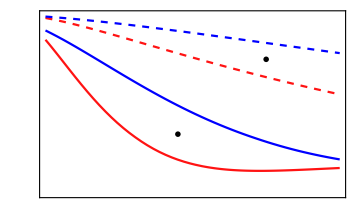

```mathematica
αplotsOpt[αlist_,T2_,η_,RE_]:=Module[{a,ℽ,b,T1, γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam, magni ,red , blue},
T1=1;(* no ZPS *)

fam = "CMU Serif";
axesLabelSize=20;
magni =axesLabelSize/12;

red   = RGBColor["#FF1313"];
blue = RGBColor["#0000FF"];

txt[α_,x_,y_] :=Graphics[ Text[Style[MaTeX["\\alpha ="<>ToString[α],Magnification->magni]],{x,y},{0,0}]];

plt = Plot[{
ℱwc[Re[√Teff[1-loss,T1,η,RE]]αlist[[1]],Re[γeff[1-loss,T1,η,RE]]],
ℱwc[Re[√Teff[1-loss,T2,η,RE]]αlist[[1]],Re[γeff[1-loss,T2,η,RE]]],
ℱwc[Re[√Teff[1-loss,T1,η,RE]]αlist[[2]],Re[γeff[1-loss,T1,η,RE]]],
ℱwc[Re[√Teff[1-loss,T2,η,RE]]αlist[[2]],Re[γeff[1-loss,T2,η,RE]]]
},{loss, 0,1},PlotRange->{0.4,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},Frame->True,FrameStyle->BlackFrame,ImageSize->Medium,PlotStyle->{red,blue,{red,Dashed},{blue,Dashed}},PlotRange->All,PlotRangeClipping->False,ImagePadding->{{65, 15}, {65, 35}},PlotRangePadding->None,
FrameLabel->{{MaTeX["\\mathcal{F}_{\\rm{w}}",Magnification->magni],None},{MaTeX["{\\rm{loss\\ rate\\ }}(1-\\gamma)",Magnification->magni],Text[Style[MaTeX["T = "<>ToString[T2]<>", \\eta = "<>ToString[η]<>", R_E = "<>ToString[RE],Magnification->magni]]]}},AspectRatio->0.6,
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0.5, 0.7, 0.9, 1}}],Automatic},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0,0.2,0.4,0.6,0.8,1}}],Automatic}}
];
Show[{plt,txt[2,0.45, .60
], txt[1,0.75, .85]}]
];
plot1 =αplotsOpt[{2,1},0.50,0.95,0.01]
(*Export["depend_alpha.pdf",plot1]*)
```

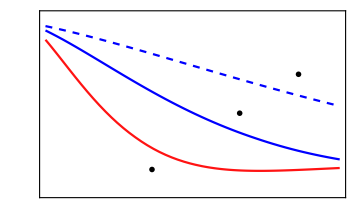

```mathematica
T2plotsOpt[α_,T2list_,η_,RE_]:=Module[{a,ℽ,b,T1, γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam, magni ,red , blue},
T1=1;(* no ZPS *)

fam = "CMU Serif";
axesLabelSize=20;
magni =axesLabelSize/12;

red   = RGBColor["#FF1313"];
blue = RGBColor["#0000FF"];

txt[T2_,x_,y_] :=Graphics[ Text[Style[MaTeX["T ="<>ToString[T2],Magnification->magni]],{x,y},{0,0}]];

plt = Plot[{
ℱwc[Re[√Teff[1-loss,T1,η,RE]]α,Re[γeff[1-loss,T1,η,RE]]],
ℱwc[Re[√Teff[1-loss,T2list[[1]],η,RE]]α,Re[γeff[1-loss,T2list[[1]],η,RE]]],
ℱwc[Re[√Teff[1-loss,T2list[[2]],η,RE]]α,Re[γeff[1-loss,T2list[[2]],η,RE]]]
},{loss, 0,1},PlotRange->{0.4,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},Frame->True,FrameStyle->BlackFrame,ImageSize->Medium,PlotStyle->{red,blue,{blue,Dashed},{blue,DotDashed}},PlotRange->All,PlotRangeClipping->False,ImagePadding->{{65, 15}, {65, 35}},PlotRangePadding->None,
FrameLabel->{{MaTeX["\\mathcal{F}_{\\rm{w}}",Magnification->magni],None},{MaTeX["{\\rm{loss\\ rate\\ }}(1-\\gamma)",Magnification->magni],Text[Style[MaTeX["\\alpha = "<>ToString[α]<>", \\eta = "<>ToString[η]<>", R_E = "<>ToString[RE],Magnification->magni]]]}},AspectRatio->0.6,
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0.5, 0.7, 0.9, 1}}],Automatic},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0,0.2,0.4,0.6,0.8,1}}],Automatic}}
];
Show[{plt,txt[1,1- .638, .482],txt[0.5,0.66, .67],txt[0.25,0.86, .80]}]
];
plot2 = T2plotsOpt[2,{0.5,0.25},0.95,0.01]
(*Export["depend_T.pdf",plot2]*)
```

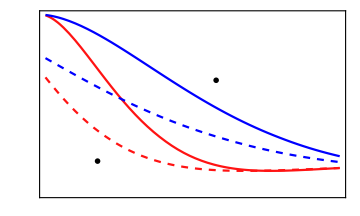

```mathematica
ηplotsOpt[α_,T2_,ηlist_,RE_]:=Module[{a,ℽ,b,T1, γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam, magni ,red , blue},
T1=1;(* no ZPS *)

fam = "CMU Serif";
axesLabelSize=20;
magni =axesLabelSize/12;

red   = RGBColor["#FF1313"];
blue = RGBColor["#0000FF"];

txt[η_,x_,y_] :=Graphics[ Text[Style[MaTeX["\\eta ="<>ToString[η],Magnification->magni]],{x,y},{0,0}]];

plt = Plot[{
ℱwc[Re[√Teff[1-loss,T1,ηlist[[1]],RE]]α,Re[γeff[1-loss,T1,ηlist[[1]],RE]]],
ℱwc[Re[√Teff[1-loss,T2,ηlist[[1]],RE]]α,Re[γeff[1-loss,T2,ηlist[[1]],RE]]],
ℱwc[Re[√Teff[1-loss,T1,ηlist[[2]],RE]]α,Re[γeff[1-loss,T1,ηlist[[2]],RE]]],
ℱwc[Re[√Teff[1-loss,T2,ηlist[[2]],RE]]α,Re[γeff[1-loss,T2,ηlist[[2]],RE]]]
},{loss, 0,1},PlotRange->{0.4,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},Frame->True,FrameStyle->BlackFrame,ImageSize->Medium,PlotStyle->{red,blue,{red,Dashed},{blue,Dashed},{red,DotDashed},{blue,DotDashed}},PlotRange->All,PlotRangeClipping->False,ImagePadding->{{65, 15}, {65, 35}},PlotRangePadding->None,
FrameLabel->{{MaTeX["\\mathcal{F}_{\\rm{w}}",Magnification->magni],None},{MaTeX["{\\rm{loss\\ rate\\ }}(1-\\gamma)",Magnification->magni],Text[Style[MaTeX["\\alpha = "<>ToString[α]<>", T = "<>ToString[T2]<>", R_E = "<>ToString[RE],Magnification->magni]]]}},AspectRatio->0.6,
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0.5, 0.7, 0.9, 1}}],Automatic},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0,0.2,0.4,0.6,0.8,1}}],Automatic}}
];
Show[{plt, txt[ηlist[[2]],.177, .51],txt[ηlist[[1]],0.58, 0.78]}]
];
plot3 = ηplotsOpt[2,0.5,{1,0.90},0.01]
(*Export["depend_eta.pdf",plot3]*)
```

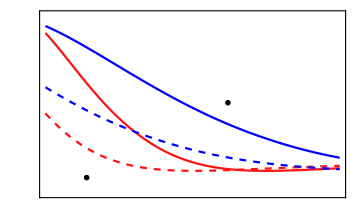

```mathematica
REplotsOpt[α_,T2_,η_,RElist_]:=Module[{a,ℽ,b,T1, γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam, magni ,red , blue},
T1=1;(* no ZPS *)

fam = "CMU Serif";
axesLabelSize=20;
magni =axesLabelSize/12;

red   = RGBColor["#FF1313"];
blue = RGBColor["#0000FF"];

txt[RE_,x_,y_] :=Graphics[ Text[Style[MaTeX["R_E ="<>ToString[RE],Magnification->magni]],{x,y},{0,0}]];

plt = Plot[{
ℱwc[Re[√Teff[1-loss,T1,η,RElist[[1]]]]α,Re[γeff[1-loss,T1,η,RElist[[1]]]]],
ℱwc[Re[√Teff[1-loss,T2,η,RElist[[1]]]]α,Re[γeff[1-loss,T2,η,RElist[[1]]]]],
ℱwc[Re[√Teff[1-loss,T1,η,RElist[[2]]]]α,Re[γeff[1-loss,T1,η,RElist[[2]]]]],
ℱwc[Re[√Teff[1-loss,T2,η,RElist[[2]]]]α,Re[γeff[1-loss,T2,η,RElist[[2]]]]]
},{loss, 0,1},PlotRange->{0.4,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},Frame->True,FrameStyle->BlackFrame,ImageSize->Medium,PlotStyle->{red,blue,{red,Dashed},{blue,Dashed},{red,DotDashed},{blue,DotDashed}},PlotRange->All,PlotRangeClipping->False,ImagePadding->{{65, 15}, {65, 35}},PlotRangePadding->None,
FrameLabel->{{MaTeX["\\mathcal{F}_{\\rm{w}}",Magnification->magni],None},{MaTeX["{\\rm{loss\\ rate\\ }}(1-\\gamma)",Magnification->magni],Text[Style[MaTeX["\\alpha = "<>ToString[α]<>", T = "<>ToString[T2]<>", \\eta = "<>ToString[η],Magnification->magni]]]}},AspectRatio->0.6,
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0.5, 0.7, 0.9, 1}}],Automatic},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0,0.2,0.4,0.6,0.8,1}}],Automatic}}
];
Show[{plt,  txt[RElist[[1]],0.62, .705],txt[RElist[[2]],0.140, 0.455]}]
];
plot4 = REplotsOpt[2,0.5,0.95,{0, 0.10}]
(*Export["depend_RE.pdf",plot4]*)
```